```mathematica
AppendTo[$Path,"~/projects/KnotTheory/trunk/"];
```

```mathematica
<<KnotTheory`
```

Loading KnotTheory` version of February 5, 2013, 3:48:46.4762.
Read more at http://katlas.org/wiki/KnotTheory.

KnotTheory::loading: Loading precomputed data in "PD4Knots`".

KnotTheory::credits: "DrawPD was written by Emily Redelmeier at the University of Toronto in the summers of 2003 and 2004."

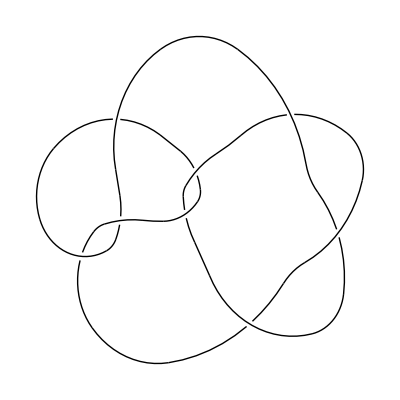

```mathematica
DrawPD[Knot[8,19]]
```

```mathematica
RotateBox[X_,0]:=X
RotateBox[RotateBox[X_,k_],l_]:=RotateBox[X,k+l]
```

```mathematica
ClearAll[PlanarDiagram]
```

```mathematica
SetAttributes[PlanarDiagram,{Flat,Orderless,OneIdentity}]
```

```mathematica
PlanarDiagram[Box[{a_,a_,b___},X_]]:=PlanarDiagram[Box[{b},Stitch[X]]]
PlanarDiagram[Box[{a__,b_,b_,c___},X_]]:=PlanarDiagram[Box[{b,b,c,a},RotateBox[X,Length[{a}]]]]
```

```mathematica
PlanarDiagram[Box[{a_,b_,c_,d_},X_],Box[{d_,c_,e___},Y_]]:=PlanarDiagram[Box[{a,b,e},Multiply[2][X,Y]]]
PlanarDiagram[Box[{a___,b_,c_,d___},X_],Box[{e___,c_,b_,f___},Y_]]:=PlanarDiagram[Box[{d,a,b,c},RotateBox[X,-Length[{d}]]],Box[{c,b,f,e},RotateBox[Y,Length[{e}]]]]
PlanarDiagram[Box[{a_,b___,c_},X_],Box[{d___,a_,c_,e___},Y_]]:=PlanarDiagram[Box[{b,c,a},RotateBox[X,1]],Box[{a,c,e,d},RotateBox[Y,Length[{d}]]]]
PlanarDiagram[Box[{a___,b_,c_,d__},X_],Box[{b_,e___,c_},Y_]]:=PlanarDiagram[Box[{d,a,b,c},RotateBox[X,-Length[{d}]]],Box[{c,b,e},RotateBox[Y,-1]]]
PlanarDiagram[Box[{a_,b___,c_},X_],Box[{c_,d___,a_},Y_]]:=PlanarDiagram[Box[{b,c,a},RotateBox[X,1]],Box[{a,c,d},RotateBox[Y,-1]]]
```

```mathematica
PlanarDiagram[Box[{a___,b_,c___},X_],Box[{d___,b_,e___},Y_]]:=PlanarDiagram[Box[{c,a,e,d},Multiply[1][RotateBox[X,-Length[{c}]],RotateBox[Y,Length[{d}]]]]]
```

```mathematica
PlanarDiagram[p_OPD]:=PlanarDiagram@@(p/.{Xp[a_,b_,c_,d_]:>Box[{c,d,a,b},Xp],Xn[a_,b_,c_,d_]:>Box[{b,c,d,a},Xn]})
```

```mathematica
PlanarDiagram[unlink=OPD[Xn[1,3,2,4],Xp[2,3,1,4]]]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][Xn,Xp],1]]]]]

```mathematica
OPD[PD[crossings___]]:=OPD[crossings]/.{X[i_,j_,k_,l_]/;(j-l==1||l-j>1):>Xp[i,j,k,l],X[i_,j_,k_,l_]/;(l-j==1||j-l>1):>Xn[i,j,k,l]}
OPD[K_Knot]:=OPD[PD[K]]
OPD[L_Link]:=OPD[PD[L]]
```

```mathematica
PlanarDiagram[K:(_Knot|_Link)]:=PlanarDiagram[OPD[K]]
```

```mathematica
PlanarDiagram[Knot[8,19]]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][Xp,Multiply[2][RotateBox[Multiply[2][RotateBox[Xp,-1],RotateBox[Xp,-1]],-1],RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Xp,-1],RotateBox[Xp,-1]],-1],RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Xp,-1],RotateBox[Xp,-1]],-2],RotateBox[Xp,1]],-1]],1]]],1]]]]]

```mathematica
(PlanarDiagram/@AllKnots[8])⟦All,1,1⟧
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{3,13,2,14},{5,13,6,12},{3,9,4,8},{},{},{}}

```mathematica
Cases[AllKnots[8],K_/;PlanarDiagram[K]⟦1,1⟧≠{}]
```

{Knot[8,16],Knot[8,17],Knot[8,18]}

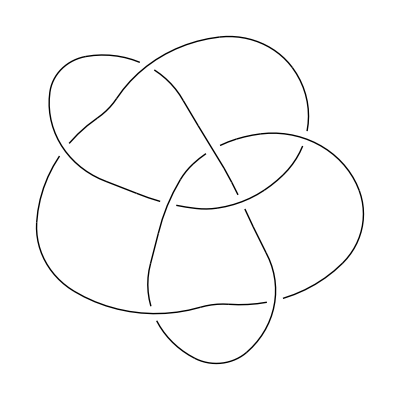

```mathematica
DrawPD[Knot[8,16]]
```

```mathematica
PlanarDiagram[Knot[8,16]]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][RotateBox[Stitch[RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Xn,-1],RotateBox[Xn,-1]],-2],RotateBox[Multiply[2][Multiply[2][RotateBox[Xn,-1],RotateBox[Xn,-1]],RotateBox[Multiply[2][RotateBox[Xn,-2],RotateBox[Multiply[1][RotateBox[Xp,-1],RotateBox[Xp,3]],2]],1]],4]],1]],2],RotateBox[Xp,-1]],1]]]]]

```mathematica
Clear[QESRotation,QESBraiding,QESInverseBraiding,QESCupCap,QESCap,QESCup,QESI,QESH,QESFork,QESFuse]
```

```mathematica
QESRotation[n_]:=QESRotation[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-rotation-matrix.m"}]];
QESRotation[n_,k_]/;k<0∨k≥n:=QESRotation[n,Mod[k,n]]
QESRotation[n_,0]:=IdentityMatrix[Length[QESRotation[n]]]
QESRotation[n_,1]:=QESRotation[n]
QESRotation[n_,k_]:=QESRotation[n,k]=Together[QESRotation[n].QESRotation[n,k-1]]
QESBraiding[n_]:=QESBraiding[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-braiding-matrix.m"}]];
QESInverseBraiding[n_]:=QESInverseBraiding[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-inverse-braiding-matrix.m"}]];
QESCupCap[n_]:=QESCupCap[n]=Together[QESCup[n-2].QESCap[n]]
QESCup[n_]:=QESCup[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-cup-matrix.m"}]]
QESCap[2]={{d}};
QESCap[n_]:=QESCap[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-cap-matrix.m"}]]
QESI[n_]:=QESI[n]=Together[QESFork[n-1].QESFuse[n]]
QESFork[n_]:=QESFork[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-fork-matrix.m"}]]
QESFuse[n_]:=QESFuse[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-fuse-matrix.m"}]]
QESH[n_]:=QESH[n]=Get[FileNameJoin[{NotebookDirectory[],ToString[n]<>"-box-H-matrix.m"}]]
```

```mathematica
RotateBox[QESBox[n_][v_],k_]:=QESBox[n][Together[QESRotation[n,k].v]]
```

```mathematica
Stitch[QESBox[n_][v_]]:=QESBox[n-2][Together[QESCap[n].v]]
```

```mathematica
AddStrand[QESBox[n_][v_]]:=QESBox[n+2][Together[QESCup[n].v]]
```

```mathematica
Multiply[2][QESBox[4][w_],QESBox[n_][v_]]:=QESBox[n][Together[Together[w.{QESCupCap[n],IdentityMatrix[Length[v]],QESI[n],QESH[n],QESBraiding[n]}].v]]
```

```mathematica
Multiply[1][b1:QESBox[4][w_],b2:QESBox[4][v_]]:=Multiply[2][b1,RotateBox[AddStrand[RotateBox[b1,-1]],1]]
```

```mathematica
(* TODO! *)
```

```mathematica
Multiply[1][QESBox[4][{1,0,0,0,0}],QESBox[4][{1,0,0,0,0}]]
```

Get::noopen: Cannot open "/Users/scott/projects/toolkit/algebra-spiders/src/main/mathematica/4-box-cup-matrix.m".

Get::noopen: Cannot open "/Users/scott/projects/toolkit/algebra-spiders/src/main/mathematica/5-box-fork-matrix.m".

Get::noopen: Cannot open "/Users/scott/projects/toolkit/algebra-spiders/src/main/mathematica/6-box-H-matrix.m".

General::stop: Further output of Get :: noopen will be suppressed during this calculation.

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot :: rect will be suppressed during this calculation.

QESBox[6][1]
 |  |  |  |

```mathematica
QESBraiding[4]⟦All,2⟧
```

{0,0,0,0,1}

```mathematica
QESInverseBraiding[4]⟦All,2⟧
```

{-((-1+v)^3 (1+v)^3 (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4) (1-v+v^2-v^3+v^4) (1+v+v^2+v^3+v^4))/(v^10 (1+d v^2+v^4)),((-1+v)^3 (1+v)^3 (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4) (1-v+v^2-v^3+v^4) (1+v+v^2+v^3+v^4))/(v^10 (1+d v^2+v^4)),((-1+v) (1+v) (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4) (1+d v^8+v^16))/(v^12 (1+d v^2+v^4)),-((-1+v) (1+v) (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4) (1+d v^8+v^16))/(v^12 (1+d v^2+v^4)),1}

```mathematica
PlanarDiagram[unlink=OPD[Xn[1,3,2,4],Xp[2,3,1,4]]]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][Xn,Xp],1]]]]]

```mathematica
PD[OPD[f___]]:=Module[{pairs,rules,n=0,cycles},
pairs = Unordered@@(Join@@({f}/.{Xp[i_,j_,k_,l_]:>{{i,k},{l,j}},Xn[i_,j_,k_,l_]:>{{i,k},{j,l}}}));
cycles=List@@(pairs//.Unordered[{x___,y_},{y_,z___}]:>Unordered[{x,y,z}]);
rules=#->++n&/@Flatten[cycles];
PD[f]/.rules/.{Xp|Xn->X}
]
```

```mathematica
QESInvariant[K:(_Knot|_Link|_PD|_OPD)]:=(PlanarDiagram[K]/.{Xp->QESBox[4][QESBraiding[4]⟦All,2⟧],Xn->QESBox[4][QESInverseBraiding[4]⟦All,2⟧]})/.PlanarDiagram[Box[{},QESBox[0][{z_}]]]:>Together[z]
```

```mathematica
Multiply[2][RotateBox[Xn,-1],RotateBox[Xn,-1]]/.{Xp->QESBox[4][QESBraiding[4]⟦All,2⟧],Xn->QESBox[4][QESInverseBraiding[4]⟦All,2⟧]}
```

QESBox[4][{((-1+v)^2 (1+v)^2 (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4) (1-v+v^2-v^3+v^4) (1+v+v^2+v^3+v^4) (1-v^4+v^6))/(v^2 (1+d v^2+v^4)),(1+v^2+v^4-v^8-v^10-2 v^12+d v^12+v^18+v^20+v^22)/(v^10 (1+d v^2+v^4)),((-1+v)^2 (1+v)^2 (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4) (1+d v^8+v^16))/(v^8 (1+d v^2+v^4)),((-1+v) (1+v) (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4) (1+d v^8+v^16))/(v^10 (1+d v^2+v^4)),((-1+v)^2 (1+v)^2 (1+v^2) (1-v+v^2) (1+v+v^2) (1+v^4) (1-v^2+v^4) (1-v+v^2-v^3+v^4) (1+v+v^2+v^3+v^4))/(v^10 (1+d v^2+v^4))}]

```mathematica
QESInvariant[unlink]
```

d^2

```mathematica
PlanarDiagram[Knot[8,19]]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][Xp,Multiply[2][RotateBox[Multiply[2][RotateBox[Xp,-1],RotateBox[Xp,-1]],-1],RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Xp,-1],RotateBox[Xp,-1]],-1],RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Xp,-1],RotateBox[Xp,-1]],-2],RotateBox[Xp,1]],-1]],1]]],1]]]]]

```mathematica
PlanarDiagram[Knot[3,1]]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Xn,-1],RotateBox[Xn,-1]],-2],RotateBox[Xn,1]],1]]]]]

```mathematica
PlanarDiagram[Knot[4,1]]
```

PlanarDiagram[Box[{},Stitch[Stitch[RotateBox[Multiply[2][RotateBox[Multiply[2][RotateBox[Xn,-2],Xn],-2],RotateBox[Multiply[2][RotateBox[Xp,-2],Xp],1]],1]]]]]

```mathematica
QESInvariant[Knot[3,1]]
```

-1/(v^32 (1+d v^2+v^4)^2)d (-1-2 v^4-v^8+v^10+v^12-2 d v^12+v^14-2 d v^14+2 v^16-3 d v^16-2 d v^18-2 v^22-v^24+6 d v^24-2 d^2 v^24-4 v^26+2 d v^26-d^2 v^26-v^28+5 d v^28-2 d^2 v^28-2 v^30-d^2 v^30+v^34-6 d v^34+2 d^2 v^34+v^36-5 d v^36+2 d^2 v^36+3 v^38-6 d v^38+2 d^2 v^38+v^40-5 d v^40+2 d^2 v^40+v^42+2 d v^42-v^44-v^46+6 d v^46-2 d^2 v^46-6 v^48+3 d v^48-d^2 v^48+4 d v^50-d^2 v^50-4 v^52+3 d v^52+2 v^54+d^2 v^54+v^56+4 v^58-2 d v^58+4 v^60-d v^60+2 v^62+3 v^64-v^66-3 v^70-d v^72-2 v^74)

```mathematica
QESInvariant[Knot[4,1]]
```

1/(v^44 (1+d v^2+v^4)^3)d (2+d v^2+5 v^4+d v^6+4 v^8-4 v^10-2 v^12+d v^12-8 v^14+2 d v^14+d^2 v^14-9 v^16+6 d v^16+d^2 v^16-5 v^18+2 d v^18+d^2 v^18-6 v^20+3 d v^20-d^2 v^20+6 v^22-2 d v^22-d^2 v^22+3 v^24-12 d v^24+2 d^2 v^24+19 v^26-10 d v^26-2 d^2 v^26+d^3 v^26+7 v^28-20 d v^28+5 d^2 v^28+16 v^30-7 d v^30+2 d^2 v^30-v^32-8 d v^32+2 d^2 v^32+12 d v^34-3 d^2 v^34-d^3 v^34-14 v^36+17 d v^36-5 d^2 v^36-d^3 v^36-16 v^38+30 d v^38-9 d^2 v^38-11 v^40+24 d v^40-8 d^2 v^40+d^3 v^40-15 v^42+18 d v^42-6 d^2 v^42+d^3 v^42+4 v^44+5 d v^44-d^2 v^44+2 v^46-21 d v^46+7 d^2 v^46+22 v^48-16 d v^48+8 d^2 v^48+10 v^50-40 d v^50+20 d^2 v^50-d^3 v^50+22 v^52-16 d v^52+8 d^2 v^52+2 v^54-21 d v^54+7 d^2 v^54+4 v^56+5 d v^56-d^2 v^56-15 v^58+18 d v^58-6 d^2 v^58+d^3 v^58-11 v^60+24 d v^60-8 d^2 v^60+d^3 v^60-16 v^62+30 d v^62-9 d^2 v^62-14 v^64+17 d v^64-5 d^2 v^64-d^3 v^64+12 d v^66-3 d^2 v^66-d^3 v^66-v^68-8 d v^68+2 d^2 v^68+16 v^70-7 d v^70+2 d^2 v^70+7 v^72-20 d v^72+5 d^2 v^72+19 v^74-10 d v^74-2 d^2 v^74+d^3 v^74+3 v^76-12 d v^76+2 d^2 v^76+6 v^78-2 d v^78-d^2 v^78-6 v^80+3 d v^80-d^2 v^80-5 v^82+2 d v^82+d^2 v^82-9 v^84+6 d v^84+d^2 v^84-8 v^86+2 d v^86+d^2 v^86-2 v^88+d v^88-4 v^90+4 v^92+d v^94+5 v^96+d v^98+2 v^100)

```mathematica
QESInvariant[Knot[5,1]]
```

-1/(v^52 (1+d v^2+v^4)^4)d (-1-4 v^4-6 v^8+v^10-3 v^12-4 d v^12+3 v^14-4 d v^14+3 v^16-13 d v^16+3 v^18-12 d v^18+5 v^20-14 d v^20-v^22-10 d v^22+v^24+9 d v^24-7 d^2 v^24-8 v^26+4 d v^26-9 d^2 v^26-3 v^28+39 d v^28-23 d^2 v^28-11 v^30+12 d v^30-21 d^2 v^30-2 v^32+36 d v^32-23 d^2 v^32-4 v^34-8 d v^34-9 d^2 v^34+4 v^36-5 d v^36+17 d^2 v^36-6 d^3 v^36+7 v^38-40 d v^38+30 d^2 v^38-8 d^3 v^38+8 v^40-47 d v^40+57 d^2 v^40-16 d^3 v^40+11 v^42-38 d v^42+48 d^2 v^42-16 d^3 v^42+3 v^44-38 d v^44+33 d^2 v^44-11 d^3 v^44+4 v^46+14 d v^46+3 d^2 v^46-6 d^3 v^46-10 v^48+10 d v^48-48 d^2 v^48+20 d^3 v^48-3 d^4 v^48-5 v^50+76 d v^50-63 d^2 v^50+20 d^3 v^50-2 d^4 v^50-20 v^52+37 d v^52-94 d^2 v^52+41 d^3 v^52-4 d^4 v^52-6 v^54+70 d v^54-59 d^2 v^54+26 d^3 v^54-3 d^4 v^54-14 v^56+8 d v^56-43 d^2 v^56+21 d^3 v^56-2 d^4 v^56+2 v^58-6 d v^58+32 d^2 v^58-12 d^3 v^58+2 d^4 v^58+3 v^60-54 d v^60+52 d^2 v^60-22 d^3 v^60+4 d^4 v^60+10 v^62-76 d v^62+98 d^2 v^62-42 d^3 v^62+6 d^4 v^62+14 v^64-67 d v^64+89 d^2 v^64-43 d^3 v^64+6 d^4 v^64+6 v^66-68 d v^66+52 d^2 v^66-22 d^3 v^66+3 d^4 v^66+9 v^68-3 d v^68+23 d^2 v^68-13 d^3 v^68+2 d^4 v^68-11 v^70+2 d v^70-48 d^2 v^70+22 d^3 v^70-2 d^4 v^70-3 v^72+79 d v^72-65 d^2 v^72+21 d^3 v^72-2 d^4 v^72-26 v^74+46 d v^74-93 d^2 v^74+36 d^3 v^74-4 d^4 v^74-6 v^76+88 d v^76-66 d^2 v^76+19 d^3 v^76-2 d^4 v^76-19 v^78+24 d v^78-39 d^2 v^78+14 d^3 v^78-d^4 v^78+3 v^80+17 d v^80+6 d^2 v^80-d^3 v^80+5 v^82-38 d v^82+37 d^2 v^82-8 d^3 v^82+14 v^84-51 d v^84+51 d^2 v^84-12 d^3 v^84+22 v^86-56 d v^86+52 d^2 v^86-10 d^3 v^86+12 v^88-52 d v^88+34 d^2 v^88-d^3 v^88+19 v^90-6 d v^90+20 d^2 v^90-2 d^3 v^90+d^4 v^90-8 v^92+d v^92-2 d^2 v^92+4 d^3 v^92+5 v^94+42 d v^94-11 d^2 v^94-29 v^96+34 d v^96-12 d^2 v^96-2 v^98+42 d v^98-11 d^2 v^98-25 v^100+22 d v^100-3 d^2 v^100+4 v^102+10 d v^102-d^2 v^102-d v^104+14 v^106-8 d v^106+18 v^108-6 d v^108+12 v^110-4 d v^110+16 v^112-d v^112-3 v^114+5 v^116-6 d v^116-15 v^118-4 d^2 v^118-12 d v^120-d^3 v^120-13 v^122-4 d^2 v^122-6 d v^124-4 v^126)

```mathematica
Quiet[<<QuantumGroups`]
```

Loading QuantumGroups` version 2.0
Read more at http://katlas.math.toronto.edu/wiki/QuantumGroups

Remember to set QuantumGroupsDataDirectory[] to the appropriate path, if you've downloaded precomputed data.

```mathematica
AdjointRepresentation[Subscript[A, n_]]:=Irrep[Subscript[A, n]][UnitVector[n,1]+UnitVector[n,n]]
AdjointRepresentation[G2]=Irrep[G2][UnitVector[2,2]];
AdjointRepresentation[F4]=Irrep[F4][UnitVector[4,1]];
AdjointRepresentation[E6]=Irrep[E6][UnitVector[6,2]];
AdjointRepresentation[E7]=Irrep[E7][UnitVector[7,1]];
AdjointRepresentation[E8]=Irrep[E8][UnitVector[8,8]];
```

```mathematica
TwistFactor[Γ_,Irrep[Γ_][λ_]]:=q^(KillingForm[Γ][λ,λ+2ρ[Γ]])
```

```mathematica
QESSubstitution[Γ_,V_]/;Length[DecomposeRepresentation[Γ][V⊗V]]≤5:={d->qDimension[Γ][V],v->PowerExpand[Power[TwistFactor[Γ,V],1/12]]}
```

```mathematica
QESSubstitution[Γ_]:=QESSubstitution[Γ,AdjointRepresentation[Γ]]
```

```mathematica
QESSubstitution[G2,Irrep[G2][{1,0}]]
```

{d→1+1/q^10+1/q^8+1/q^2+q^2+q^8+q^10,v→q}

```mathematica
Link[2,Alternating,1]//OPD
```

KnotTheory::loading: Loading precomputed data in "PD4Links`".

OPD[Xn[4,1,3,2],Xn[2,3,1,4]]

```mathematica
Together[QESInvariant[Link[2,Alternating,1]]/.QESSubstitution[G2,Irrep[G2][{0,1}]]]
```

((1+q^6+q^10+q^12-q^14+q^16+q^18+q^22+q^28) (1+q^8+q^12+q^14+q^16+q^18+q^20+q^22+q^24+q^26+q^28+2 q^30+q^32+q^36+2 q^38+q^40+q^42+q^44+q^46+q^48+q^50+q^52+q^54+q^56+q^60+q^68))/q^48

```mathematica
Together[QESInvariant[Knot[3,1]]/.QESSubstitution[G2,Irrep[G2][{0,1}]]]
```

1/q^54(1+q^8) (1+q^6+q^10+q^12-q^14+q^16+q^18+q^22+q^28) (1+q^12+q^14+q^16-q^20-q^22-q^24+q^28+2 q^30+q^32-q^34-2 q^36-2 q^38-q^40+q^42+2 q^44+2 q^46-2 q^50-3 q^52-2 q^54+2 q^58+3 q^60+q^62-2 q^66-q^68-q^70+2 q^74+2 q^76-q^80-q^82-q^84+q^90)

```mathematica
Together[QESInvariant[Knot[4,1]]/.QESSubstitution[G2,Irrep[G2][{0,1}]]]
```

1/q^78(1+q^8) (1+q^6+q^10+q^12-q^14+q^16+q^18+q^22+q^28) (1-q^6-q^8-q^10+q^12+3 q^14+3 q^16-3 q^20-4 q^22-4 q^24+4 q^28+8 q^30+4 q^32-2 q^34-8 q^36-9 q^38-5 q^40+4 q^42+11 q^44+11 q^46+3 q^48-7 q^50-12 q^52-11 q^54-q^56+9 q^58+15 q^60+9 q^62-q^64-11 q^66-12 q^68-7 q^70+3 q^72+11 q^74+11 q^76+4 q^78-5 q^80-9 q^82-8 q^84-2 q^86+4 q^88+8 q^90+4 q^92-4 q^96-4 q^98-3 q^100+3 q^104+3 q^106+q^108-q^110-q^112-q^114+q^120)

```mathematica
Together[QESInvariant[Knot[8,19]]/.QESSubstitution[G2,Irrep[G2][{0,1}]]]
```

1/q^96(1+q^8) (1+q^6+q^10+q^12-q^14+q^16+q^18+q^22+q^28) (1-q^10-q^12+q^16+q^18-2 q^24-2 q^26-q^28+q^30+2 q^32+2 q^34+q^36-q^38-3 q^40-3 q^42+2 q^46+3 q^48+3 q^50+q^52-2 q^54-3 q^56-2 q^58+q^60+3 q^62+4 q^64+2 q^66-2 q^70-3 q^72-q^74+q^76+2 q^78+2 q^80+q^82-q^84-2 q^86-2 q^88-q^90-q^100-q^102-q^104-q^106-q^108-q^110-q^122-q^124+q^130+q^132+q^134+q^144+q^146+q^148+q^150+q^162)

```mathematica
Together[QESInvariant[Knot[8,19]]/.QESSubstitution[E8]]
```

1/q^240(1+q^4)^2 (1-q^4+q^8-q^12+q^16) (1+q^2+q^8+q^10+q^12+q^14+q^16+q^18+q^20+q^22+2 q^24+2 q^26+q^28+q^30+2 q^32+2 q^34+2 q^36+2 q^38+2 q^40+2 q^42+2 q^44+2 q^46+2 q^48+2 q^50+2 q^52+2 q^54+2 q^56+2 q^58+2 q^60+q^62+q^64+2 q^66+2 q^68+q^70+q^72+q^74+q^76+q^78+q^80+q^82+q^84+q^90+q^92) (1-q^2-q^12+q^14-q^20+q^32-q^34+q^40-q^42+q^46+q^48-q^52+2 q^54+q^58-q^60+3 q^62+q^70+2 q^72-2 q^74+q^76+2 q^80-2 q^82-q^90-3 q^92+2 q^94-2 q^96-2 q^98-4 q^100+q^102-2 q^104-2 q^106-3 q^108-q^110-q^112-5 q^114-q^116-2 q^118-5 q^122-q^126-3 q^130-2 q^132+2 q^134-q^136+q^138-q^140+5 q^142+q^146+2 q^148+5 q^150+4 q^152+5 q^156+4 q^158+6 q^160+q^162+6 q^164+4 q^166+5 q^168+2 q^170+5 q^172+6 q^174+3 q^176+2 q^178+2 q^180+6 q^182+q^184+2 q^186+3 q^190-2 q^194+q^196-q^198-q^200-5 q^202-3 q^206-3 q^208-6 q^210-3 q^212-3 q^214-5 q^216-4 q^218-4 q^220-3 q^222-6 q^224-5 q^226-4 q^228-2 q^230-5 q^232-4 q^234-3 q^236-2 q^238-3 q^240-3 q^242-q^244-2 q^246-q^248-2 q^250+q^252-q^256+q^260+2 q^262+2 q^266+q^268+2 q^270+q^272+2 q^274+2 q^276+2 q^278+q^280+2 q^282+2 q^284+2 q^286+q^288+q^290+2 q^292+q^294+q^296+q^298+q^300+q^302+q^306+q^308+q^310+q^314)

```mathematica
TwistFactor[E6,AdjointRepresentation[E6]]
```

q^24

```mathematica
TwistFactor[E7,AdjointRepresentation[E7]]
```

q^36

```mathematica
TwistFactor[E8,AdjointRepresentation[E8]]
```

q^60